```mathematica
ClearAll["Global`*"];
```

Parameter assumptions

```mathematica
$Assumptions={ω∈Reals,χ∈Reals,κ∈Reals&&κ≥0,t∈Reals&&t≥0,s∈Reals&&s≥0,Ω∈Reals,x[t]∈Reals,p[t]∈Reals,x'[t]∈Reals,p'[t]∈Reals,ϵ1[t]∈Reals,ϵ2[t]∈Reals,α∈Reals,β∈Reals,σ∈Reals};
```

Langevin Equation

```mathematica
Le[t_,χ_,κ_,σ_]=D[a[t],t]+I*χ*σ*a[t]+κ/2*a[t]+Ω[t];
TraditionalForm[Le[t,χ,κ,σ]]
```

a'(t)+1/2 κ a(t)+ⅈ σ χ a(t)+Ω(t)

Separate in Real and imaginary part

```mathematica
LeRI[t_,χ_,κ_,σ_]=Le[t,χ,κ,σ]/.{a[t]->x[t]+I*p[t],a'[t]->x'[t]+I*p'[t],Ω[t]->ϵ1[t]+I*ϵ2[t]};
TraditionalForm[LeRI[t,χ,κ,σ]]
```

ⅈ p'(t)+1/2 κ (x(t)+ⅈ p(t))+ⅈ σ χ (x(t)+ⅈ p(t))+x'(t)+ϵ1(t)+ⅈ ϵ2(t)

Write the differential equation as a linear system

```mathematica
X[t_]={x[t],p[t]};
```

```mathematica
u[t_]={ϵ1[t],ϵ2[t]};
```

```mathematica
A=-{Grad[FullSimplify[Re[LeRI[t,χ,κ,σ]]],X[t]],Grad[FullSimplify[Im[LeRI[t,χ,κ,σ]]],X[t]]};
TraditionalForm[A]
```

(-κ/2 | σ χ
-σ χ | -κ/2)

```mathematica
B=-{Grad[FullSimplify[Re[LeRI[t,χ,κ,σ]]],u[t]],Grad[FullSimplify[Im[LeRI[t,χ,κ,σ]]],u[t]]};
TraditionalForm[B]
```

(-1 | 0
0 | -1)

Optimal control Pulse

```mathematica
Xf={α,β};
X0={0,0};
```

```mathematica
μ1=FullSimplify[Inverse[Integrate[MatrixExp[A*(s-t)].B.Transpose[B].Transpose[MatrixExp[A*(s-t)]],{t,0,s}]]];
TraditionalForm[μ1]
```

(κ (1/(ⅇ^(κ s)-1)+1) | 0
0 | κ (1/(ⅇ^(κ s)-1)+1))

```mathematica
μ2=(Xf-MatrixExp[A*s].X0);
```

```mathematica
μ=FullSimplify[μ1.μ2];
```

```mathematica
uopt[t_,s_,χ_,κ_,σ_,α_,β_]=FullSimplify[2*Transpose[B].Transpose[MatrixExp[A*(s-t)]].μ];
TraditionalForm[uopt[t,s,χ,κ,σ,α,β]]
```

{-(2 κ ⅇ^(1/2 κ (s+t)) (α cos(σ χ (s-t))-β sin(σ χ (s-t))))/(ⅇ^(κ s)-1),-(2 κ ⅇ^(1/2 κ (s+t)) (α sin(σ χ (s-t))+β cos(σ χ (s-t))))/(ⅇ^(κ s)-1)}

```mathematica
uopt[t,30,0.25,2*π*0.01,1,0.5,0][[1]]+I*uopt[t,30,0.25,2*π*0.01,1,0.5,0][[2]]
```

-0.011248 ⅇ^(0.0314159 (30+t)) Cos[0.25 (30-t)]-(0.+0.011248 ⅈ) ⅇ^(0.0314159 (30+t)) Sin[0.25 (30-t)]

```mathematica
TrigToExp[-0.011247969229737236 ⅇ^(0.031415926535897934 (30+t)) Cos[0.25 (30-t)]-(0.+0.011247969229737236 ⅈ) ⅇ^(0.031415926535897934 (30+t)) Sin[0.25 (30-t)]]
```

(0.+0. ⅈ)-(0.011248+0. ⅈ) ⅇ^((0.+0.25 ⅈ) (30-t)+0.0314159 (30+t))

```mathematica
amp[t_]=0.011247969229737236*Exp[0.031415926535897934 (30+t)];
phase[t_]=0.25 (30-t);
```

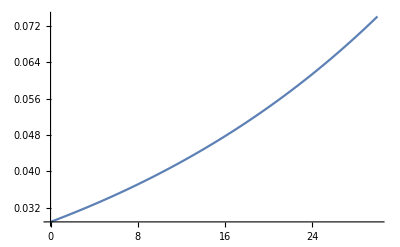

```mathematica
Plot[amp[t],{t,0,30}]
```

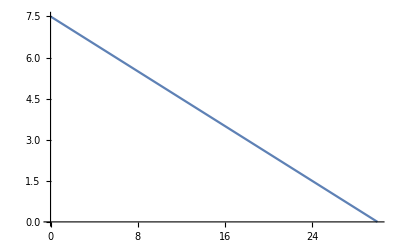

```mathematica
Plot[phase[t],{t,0,30}]
```

```mathematica
$Assumptions={ω∈Reals,χ∈Reals,κ∈Reals&&κ≥0,t∈Reals&&t≥0,s∈Reals&&s≥0,Ω∈Reals,x[t]∈Reals,p[t]∈Reals,x'[t]∈Reals,p'[t]∈Reals,ϵ1[t]∈Reals,ϵ2[t]∈Reals,α∈Reals,β∈Reals,ϕ∈Reals,σ∈Reals};
```

Langevin equations

```mathematica
Le[t_,χ_,κ_,σ_]=D[a[t],t]+I*(σ*χ)*a[t]+κ/2*a[t]+Ω[t];
Letime[t_,χ_,κ_,ϵ0_,σ_,ϕ_]=Le[t,χ,κ,σ]/.{Ω[t]->ϵ0 Sin[χ*t+ϕ]+I*ϵ0 Cos[χ*t+ϕ]};
```

```mathematica
Soltime[t_,χ_,κ_,ϵ0_,σ_,ϕ_]=FullSimplify[DSolve[{Letime[t,χ,κ,ϵ0,σ,ϕ]==0,a[0]==0},a[t],t]];
```

```mathematica
tmin[χ_,κ_,ϵ0_,α_,β_,σ_,ϕ_]:=FindRoot[Abs[Soltime[t,χ,κ,ϵ0,σ,ϕ][[1,1,2]]]==Abs[α+I*β],{t,0}]
phisol[χ_,κ_,ϵ0_,α_,β_,σ_]:=FindRoot[Soltime[tmin[χ,κ,ϵ0,α,β,σ,π/2][[1,2]],χ,κ,ϵ0,σ,ϕ][[1,1,2]]==α+I*β,{ϕ,0}]
```

```mathematica
χ=0.25;
κ=2*π*0.01;
n=1;
ϵtem=0.06;
```

minimal time:23.6025

phi:-1.18824

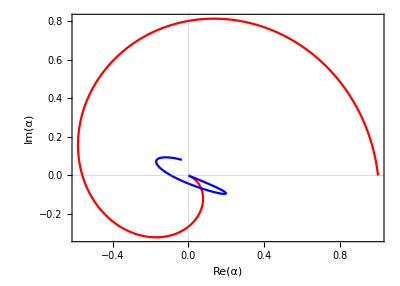

```mathematica
tmin1=tmin[χ,κ,ϵtem,n,0,1,π/2][[1,2]];
Print["minimal time:",tmin1]
ϕ1=Re[phisol[χ,κ,ϵtem,n,0,1][[1,2]]];
Print["phi:",ϕ1]
ParametricPlot[{{Re[Soltime[t,χ,κ,ϵtem,1,ϕ1][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,1,ϕ1][[1,1,2]]]},{Re[Soltime[t,χ,κ,ϵtem,-1,ϕ1][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,-1,ϕ1][[1,1,2]]]}(*{Re[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]],Im[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]]}*)},{t,0,tmin1},PlotStyle->{Red,Blue},PlotTheme->"Scientific",FrameStyle->Directive[Thickness[0.003],Black,20],FrameLabel->{"Re(α)","Im(α)"},LabelStyle->Directive[Black,16,FontFamily->"Times"]]
```

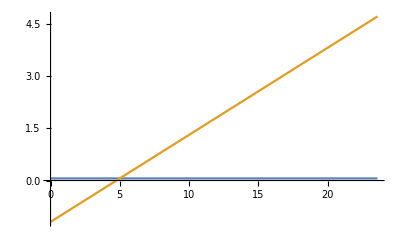

```mathematica
Plot[{ϵtem,χ*t+ϕ1},{t,0,tmin1}]
```

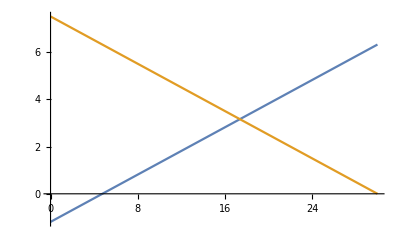

C:\Users\Mo Zhou\python file\paint\energyplot.csv

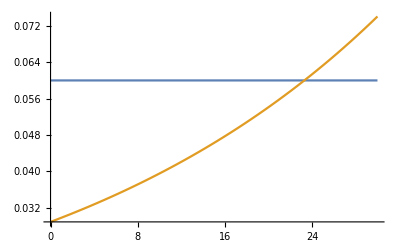

C:\Users\Mo Zhou\python file\paint\timeplot.csv

```mathematica
Plot[{χ*t+ϕ1,phase[t]},{t,0,30}]
energyopt=Table[{amp[t/1000*30],phase[t/1000*30]},{t,0,1000}];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\energyplot.csv",energyopt]
Plot[{ϵtem,amp[t]},{t,0,30}]
timeopt=Table[{ϵtem,χ*t/1000*tmin1+ϕ1},{t,0,1000}];
Export["C:\\Users\\Mo Zhou\\python file\\paint\\timeplot.csv",timeopt]
```